```mathematica
2D diffusion/deformation with a pressure gradient
```

(2 a D diffusion gradient pressure with)/deformation

```mathematica
SetOptions[ListLinePlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16}];
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->16}];
```

```mathematica
D0 =5.4*10^-7;
Q = 53.9*10^3;
R = 8.314;
T = 300.;
Diff = D0*Exp[-Q/R/T];
Na = 6.0221413 *10^23;
clinit = 5.;
VM = 7.116 * 10^-6;
NL =1.405283867341203*10^5;
WB = 9.65 * 10^3;
KT =  Exp[WB/R/T];
NT = 1.0*10^(26.6-1.5*Exp[-0.0*ep])/Na  /. {ep -> 0.};
CT = NT/(1+NL/KT/CL);
dCTdCL = D[CT,CL];
dCTdCLinit = dCTdCL /. {CL -> clinit};
Deff = 1.+dCTdCLinit ;


bulkMod = 163.33333333333333333*10^9;
shearMod = 75.38461538461539*10^9;
VH = 2.0*10^-6;
```

```mathematica
C0 = 0.0;
C1 = 4.0*10^-3; (*-3*)
C2 = 1.6*10^-2; (*4*)
C3 = 1.0*10^-2; (*10*)

U1 = (C0 + C1*(X1/(1*10^-6)) + C2*(X1/(1*10^-6))^2 + C3*(X1/(1.0*10^-6))^3)*(t/1000)*1*10^-6;
U2 = 0;
U3 = 0;
Ueval  = U1 /. {t -> 1000, X1 -> 1.0*10^-6}
```

3.×10^-8

```mathematica
x1 = X1 + U1;
x2 = X2;
x3 = X3;

F = {{D[x1,X1],D[x1,X2],D[x1,X3]},{D[x2,X1],D[x2,X2],D[x2,X3]},{D[x3,X1],D[x3,X2],D[x3,X3]}};
Finverse = Inverse[F];
Fdot = D[F,t];
J = Det[F] ;
b = F.Transpose[F] ;
devb = b - 1/3 * (b[[1,1]] + b[[2,2]] + b[[3,3]])*IdentityMatrix[3];
sigma = 0.5 * bulkMod * (J - 1/J) * IdentityMatrix[3]  + shearMod * J^(-5/3) * devb;

MatrixForm[Inverse[(Transpose[F].F)] /. {X1 -> 0.0, X2 -> 0.0, X3 -> 0.0, t-> 1000}]
(*sigma11 = (bulkMod + 4./3.*shearMod) *H[[1,1]];
sigma22 = (bulkMod - 2./3.*shearMod) *H[[1,1]];
sigma33 = (bulkMod - 2./3.*shearMod) *H[[1,1]];*)

sigma11 = sigma[[1,1]];
sigma22 = sigma[[2,2]];
sigma33 = sigma[[3,3]];

kirchhoffHydro = 1./3. * Det[F] * (sigma11 + sigma22 + sigma33);
gradKirchhoffHydro = D[kirchhoffHydro,X1];
```

(0.992048 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
F[[1,1]] /. t-> 1000
```

1+(4000.+3.2×10^10 X1+3.×10^16 X1^2)/1000000

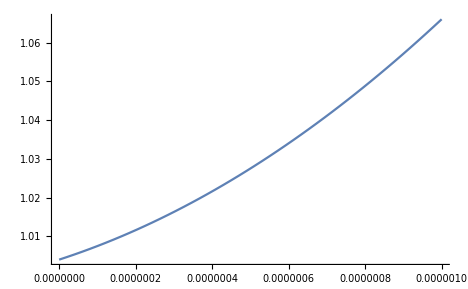

```mathematica
Plot[F[[1,1]] /. t -> 1000,{X1,0, 10^-6}]
```

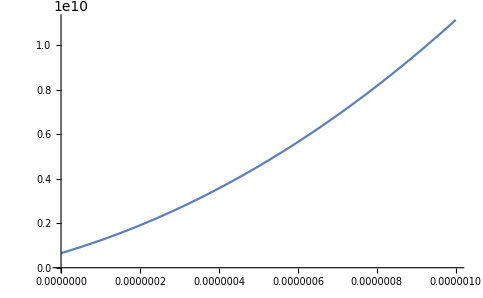

```mathematica
Plot[kirchhoffHydro /. t -> 1000,{X1,0, 10^-6}]
```

```mathematica
PdeClPress = -Diff*D[Finverse[[1,1]]^2*D[cl[X1,t],X1],X1] + Deff*D[cl[X1,t],t] +D[Diff*cl[X1,t]*VH/R/T*Finverse[[1,1]]^2*D[kirchhoffHydro,X1],X1] ;
slopeConcentration = 
ClSolution =NDSolve[{PdeClPress == 0, cl[X1,0]==clinit,cl[1*10^-6,t] == clinit, cl[0,t]==clinit*(1.+0.019*t)},cl,{X1,0,1*10^-6},{t,0,1000}, MaxStepFraction->1/100, MaxStepSize -> 1];
```

```mathematica
nbHome = NotebookDirectory[]
filenameImportOld = StringJoin[nbHome,  "blockDiffusionPressGrad_Output_Old.txt"]
dataContentPressGradOld=Import[filenameImportOld,"table"];
filenameImport = StringJoin[nbHome,  "blockDiffusionPressGrad_Output.txt"]
dataContentPressGrad=Import[filenameImport,"table"];
```

/Users/jwfoulk/Documents/Sandia2007/Tritium_GTS/finalizingTransport/press_grad/

/Users/jwfoulk/Documents/Sandia2007/Tritium_GTS/finalizingTransport/press_grad/blockDiffusionPressGrad_Output_Old.txt

/Users/jwfoulk/Documents/Sandia2007/Tritium_GTS/finalizingTransport/press_grad/blockDiffusionPressGrad_Output.txt

```mathematica
Show[Plot[Evaluate[cl[X1,1000] /. ClSolution],{X1,0,1*10^-6}, PlotRange -> All],ListLinePlot[dataContentPressGrad[[All,{1,2}]],PlotMarkers-> "*", PlotStyle -> Red],AxesLabel ->{X1,CL}, ImageSize -> 1000]
```

-Graphics-

Comments: The analytical solution (Blue) of the hydrogen diffusion equation has some slight differences to the one obtained using FEM (Red).
**note: FEM model assumes neo-hookean material.  Mathematica model now employs neo-hookean material. More work needs to be done to examine field quantities but the fields seem to checkout. Might be that we don’t nail the pressure. More work may be needed.

What is required: We need a finer mesh to get rid of the instability on the left hand side. The instability is concerning. I’m not sure where that is coming from. This will be hard to do without an analytic function specifying the deformation gradient.